# 2D First-Passage time

## Drift towards the equilibrium at (x, xh) = (0, 0) with an absorbing boundary at xh=1.

## Write down the nondimensionalized Fokker-Planck equation

```mathematica
FP= D[p[t, x, xh], t]==λ*D[xh*p[t, x, xh], x]+D[xh*p[t, x, xh], xh]-κ*D[x*p[t, x, xh],xh]+λ*D[p[t, x, xh],{x,2}]+D[p[t, x, xh],{xh,2}]
```

p^(1,0,0)[t,x,xh]==p[t,x,xh]+xh p^(0,0,1)[t,x,xh]-x κ p^(0,0,1)[t,x,xh]+p^(0,0,2)[t,x,xh]+xh λ p^(0,1,0)[t,x,xh]+λ p^(0,2,0)[t,x,xh]

## Choose the parameter values

```mathematica
λs = {0.05, 0.1, 0.2, 0.5, 1};
κs = {0.05, 0.1,0.2,0.5, 1};
params = Flatten[Table[{λ->l, κ->k}, {l, λs}, {k, κs}], 1]
legend =  Flatten[Table["λ="<>ToString[l]<>"; "<> "κ="<>ToString[k], {l, λs},{k, κs}], 1];
```

{{λ→0.05,κ→0.05},{λ→0.05,κ→0.1},{λ→0.05,κ→0.2},{λ→0.05,κ→0.5},{λ→0.05,κ→1},{λ→0.1,κ→0.05},{λ→0.1,κ→0.1},{λ→0.1,κ→0.2},{λ→0.1,κ→0.5},{λ→0.1,κ→1},{λ→0.2,κ→0.05},{λ→0.2,κ→0.1},{λ→0.2,κ→0.2},{λ→0.2,κ→0.5},{λ→0.2,κ→1},{λ→0.5,κ→0.05},{λ→0.5,κ→0.1},{λ→0.5,κ→0.2},{λ→0.5,κ→0.5},{λ→0.5,κ→1},{λ→1,κ→0.05},{λ→1,κ→0.1},{λ→1,κ→0.2},{λ→1,κ→0.5},{λ→1,κ→1}}

## Set up the mesh, boundary conditions, and initial condition

```mathematica
xf=15;
tf=12;
icPos = {5, 5};
icVar = {{1/(2κ)+((1+κ) λ)/(2κ),1/2},{1/2,(1+κ)/2}}/.params[[25]] (*Choose widest s.s. distribution of the parameter values*)
ic0 = N[Table[PDF[MultinormalDistribution[icPos,icVar], {x, xh}], {i, params}]];
bcs = {p[t,-xf, xh]==0,
           p[t, xf, xh]==0,
           p[t, x, xf]==0,
           p[t, x, 1]==0
}

Needs["NDSolve`FEM`"]
mesh=ToElementMesh[Rectangle[{-xf, 1}, {xf, xf}],MaxCellMeasure->0.1 ]
mesh["Wireframe"]
```

{{3/2,1/2},{1/2,1}}

## Calculate the probability distribution and the flux through the boundary

```mathematica
NDSolverParams[param_, ic_] :=Module[{N},
N = NDSolve[Join[{(FP/. param),p[0, x,xh]== ic}, bcs],
                                   p,{t,0,tf},Element[{x, xh}, mesh], 
Method->{"PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"FiniteElement"}}}];
Return[p/.N[[1]]];
]
```

```mathematica
sols=MapThread[NDSolverParams, {params, ic0}];
flux = Table[Derivative[0,0,1][sol], {sol, sols}];
```

```mathematica
Manipulate[Plot3D[sols[[25]][t, x, xh], {x, -xf,xf}, {xh, 1, xf}, AxesLabel->{x, xh}, PlotRange->{-0.01, 0.3}, PlotLegends->Automatic, ColorFunction->ColorData[{"CherryTones",{-0.01,0.2}}],ColorFunctionScaling->False], {t, 0, tf}]
Manipulate[ContourPlot[sols[[4]][t, x, xh], {x, -xf,xf}, {xh, 1, xf}, AxesLabel->{x, xh},PlotRange->{-0.01, 0.3}, ColorFunction->ColorData[{"CherryTones",{-0.01,0.2}}],ColorFunctionScaling->False, PlotLegends->Automatic], {t, 0, tf}]
```

Part::partw: Part 25 of {«1»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 25 of {«1»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 25 of {«1»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 25 of {«1»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 25 of {«1»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 25 of {«1»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 25 of {«1»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 25 of {«1»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 25 of {InterpolatingFunction[{{-15.,15.},{1.,15.}},{5,4225,0,{25912,0},{3,3},0,0,0,0,Indeterminate&,{},{},False},{ElementMesh[«1»]},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«25862»},{Automatic}],«8»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 25 of {InterpolatingFunction[{{-15.,15.},{1.,15.}},{5,4225,0,{25912,0},{3,3},0,0,0,0,Indeterminate&,{},{},False},{ElementMesh[«1»]},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«25862»},{Automatic}],«8»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 25 of {InterpolatingFunction[{{-15.,15.},{1.,15.}},{5,4225,0,{25912,0},{3,3},0,0,0,0,Indeterminate&,{},{},False},{ElementMesh[«1»]},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«25862»},{Automatic}],«8»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 25 of {InterpolatingFunction[{{-15.,15.},{1.,15.}},{5,4225,0,{25912,0},{3,3},0,0,0,0,Indeterminate&,{},{},False},{ElementMesh[«1»]},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«25862»},{Automatic}],«8»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 25 of {InterpolatingFunction[{{-15.,15.},{1.,15.}},{5,4225,0,{25912,0},{3,3},0,0,0,0,Indeterminate&,{},{},False},{ElementMesh[«1»]},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«25862»},{Automatic}],«8»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 25 of {InterpolatingFunction[{{-15.,15.},{1.,15.}},{5,4225,0,{25912,0},{3,3},0,0,0,0,Indeterminate&,{},{},False},{ElementMesh[«1»]},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«25862»},{Automatic}],«8»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 25 of {InterpolatingFunction[{{-15.,15.},{1.,15.}},{5,4225,0,{25912,0},{3,3},0,0,0,0,Indeterminate&,{},{},False},{ElementMesh[«1»]},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«25862»},{Automatic}],«8»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 25 of {InterpolatingFunction[{{-15.,15.},{1.,15.}},{5,4225,0,{25912,0},{3,3},0,0,0,0,Indeterminate&,{},{},False},{ElementMesh[«1»]},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«25862»},{Automatic}],«8»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 25 of {InterpolatingFunction[{{-15.,15.},{1.,15.}},{5,4225,0,{25912,0},{3,3},0,0,0,0,Indeterminate&,{},{},False},{ElementMesh[«1»]},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«25862»},{Automatic}],«8»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 25 of {InterpolatingFunction[{{-15.,15.},{1.,15.}},{5,4225,0,{25912,0},{3,3},0,0,0,0,Indeterminate&,{},{},False},{ElementMesh[«1»]},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«25862»},{Automatic}],«8»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 25 of {InterpolatingFunction[{{-15.,15.},{1.,15.}},{5,4225,0,{25912,0},{3,3},0,0,0,0,Indeterminate&,{},{},False},{ElementMesh[«1»]},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«25862»},{Automatic}],«8»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

## Integrate the flux in t to get q(x)

At a given value of x, integrate in time

```mathematica
xrange = N[Range[-xf, xf, 2*xf/50]]
```

{-15.,-14.4,-13.8,-13.2,-12.6,-12.,-11.4,-10.8,-10.2,-9.6,-9.,-8.4,-7.8,-7.2,-6.6,-6.,-5.4,-4.8,-4.2,-3.6,-3.,-2.4,-1.8,-1.2,-0.6,0.,0.6,1.2,1.8,2.4,3.,3.6,4.2,4.8,5.4,6.,6.6,7.2,7.8,8.4,9.,9.6,10.2,10.8,11.4,12.,12.6,13.2,13.8,14.4,15.}

```mathematica
nintxsolve[xr_, s_]:=Module[{t, x},
n =Table[NDSolveValue[{g'[t]==s[t, x, 1],g[0]==0},g,{t,0,tf}, Method->{"MethodOfLines","SpatialDiscretization"->{"FiniteElement"}}][tf], {x, xr}];
Return[n];
];
```

```mathematica
xvals = Table[nintxsolve[xrange,flu], {flu, flux}];
```

Interpolate to get the distribution in x

```mathematica
X=Table[Interpolation[Transpose@{xrange, xval}][x], {xval, xvals}];
```

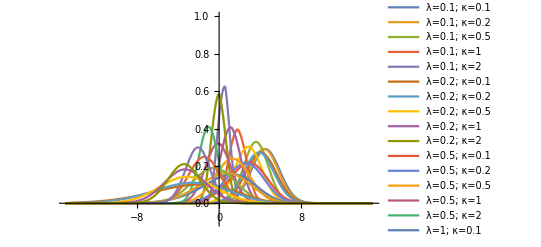

```mathematica
Plot[X, {x, -xf, xf}, PlotLegends->legend, PlotRange->{-0.1, 1}]
```

```mathematica
norms = Table[NIntegrate[xp, {x, -xf, xf}, WorkingPrecision->16], {xp, X}]
means = Table[NIntegrate[xp*x, {x, -xf, xf}, WorkingPrecision->16], {xp, X}]
second = Table[NIntegrate[xp*x*x, {x, -xf, xf}, WorkingPrecision->16], {xp, X}];
vars = second-means^2
diff = vars/means;
```

{1.0144,1.00878,0.981853,0.838827,0.907891,1.0113,1.01195,1.00943,1.00324,0.999346,1.00838,1.00324,1.00891,0.998844,0.954698,0.996696,1.00786,0.99658,0.96926,0.897804,0.988328,0.985858,0.965421,0.916181,0.819516}

{4.592428045769071,4.453510497513735,3.541662793152116,1.51904680278048,0.4134105518923136,4.110748778774828,3.917007957625881,2.874468733147726,1.131323284992863,-0.05549498306318004,2.762691344789191,2.432217213921565,1.303180679706346,-0.07353979094987315,-0.9992590215829252,0.6960462547257095,0.3855616242648943,-0.5021097176176257,-1.368951126317595,-1.868879819732343,-2.831690210087625,-2.877314659000542,-2.992881952377459,-3.027867523547122,-2.827705639501402}

{1.6783089398332,1.7561882630913,1.6249649176721,1.05544983103586,0.312292228783868,2.0865647228472,2.0649983294614,1.7126923466648,0.981882024094788,0.466893087789821,3.57300207904672,3.54102577199533,2.82280100214749,1.57665332826189,0.872348982293455,6.919030438125,6.33771889421883,4.37483426966154,2.45483628833476,1.69918317512612,14.826803666522,12.2351556491764,7.46413505984124,4.66618908868067,3.78645176973895}

```mathematica
λs = { 0.1, 0.2, 0.5, 1, 2};
σs = {0.1, 0.2, 0.5, 1, 2};
grid = Flatten[Table[{l, s}, {l, λs}, {s, σs}], 1];
v = Table[{va}, {va, vars}];
```

```mathematica
varArray = ArrayReshape[vars, {5, 5}];
meanArray = ArrayReshape[means, {5, 5}];
diffArray = ArrayReshape[diff, {5, 5}];
```

```mathematica
xticks = Transpose[{{1, 2, 3, 4, 5}, λs}];
yticks = Transpose[{{1, 2, 3, 4, 5}, σs}];
```

```mathematica
ArrayPlot[varArray, ColorFunction->(Blend[{White,Blue},#]&), PlotLegends->{Placed[BarLegend[Automatic,Automatic,LegendLabel->"var(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]

ArrayPlot[meanArray, ColorFunction->(Blend[{White,Blue},#]&), PlotLegends->{Placed[BarLegend[Automatic,Automatic,LegendLabel->"mean(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]

ArrayPlot[diffArray, ColorFunction->(Blend[{White,Blue},#]&), PlotLegends->{Placed[BarLegend[Automatic,Automatic,LegendLabel->"var(x)/mean(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]
```

-Graphics-

-Graphics-

-Graphics-

## Integrate to get the survival probability and first-passage times

```mathematica
nintrange[tr_, s_]:=Module[{x, xh},
n = Table[NIntegrate[s[x,xh,t], {x,xh}∈s["ElementMesh"],  Method->"InterpolationPointsSubdivision"],{t, tr}];
Return[n];
];trange = N[Range[0, tf, tf/50]];
```

```mathematica
S= Table[nintrange[trange,sol], {sol, sols}];
```

NIntegrate::femonly: Method InterpolationPointsSubdivision is not applicable for this region domain. Continuing with the "FiniteElement" method.

General::stop: Further output of NIntegrate::femonly will be suppressed during this calculation.

```mathematica
s=Table[Interpolation[Transpose@{trange, Sp}][t], {Sp, S}];
f = Table[-D[sp, t], {sp, s}];
```

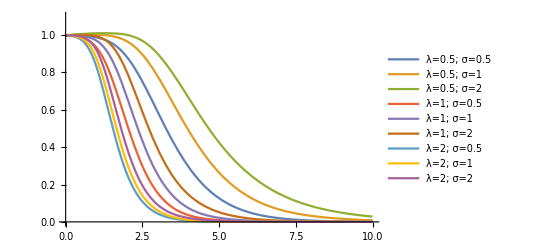

```mathematica
Plot[s,{t, 0, tf}, PlotRange->{0,1.1}, PlotLegends->legend]
```

## Calculate first-passage time probability

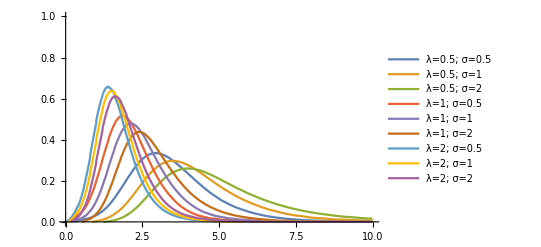

```mathematica
Plot[f,{t, 0, tf}, PlotRange->{0, 1} , PlotLegends->legend]
```

```mathematica
norms = Table[NIntegrate[fp, {t, 0, tf}], {fp, f}]
means = Table[NIntegrate[fp*t, {t, 0, tf}], {fp, f}]
second = Table[NIntegrate[fp*t*t, {t, 0, tf}], {fp, f}]
vars = second-means^2
```

{0.996601,0.988501,0.968595,0.997091,0.997098,0.996506,0.99702,0.997011,0.997015}

{3.45462,4.16734,4.76701,2.15921,2.49471,2.90643,1.63569,1.75965,1.93072}

{13.817,19.8175,25.9578,5.47297,7.21248,9.71744,3.18336,3.64939,4.37198}

{1.88255,2.45074,3.23341,0.810779,0.988891,1.27009,0.507871,0.553031,0.644305}